```mathematica
Quit[]
```

## Tensorial Part

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2018, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2018, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)

$CommuteCovDsOnScalars=True;

DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,s,u,v,μ,ν,κ,λ}]

DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]

Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];

DefMetricPerturbation[metric,metpert,ϵ];
PrintAs[metpert]^="h";

DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensorPerturbation[PertPhi[LI[order]],Phi[],M4,PrintAs->"δφ"]

DefTensor[PhiC[],M4,PrintAs->"φ^*"]
DefTensorPerturbation[PertPhiC[LI[order]],PhiC[],M4,PrintAs->"δφ^*"]
```

We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^*

```mathematica
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[a][Phi[]]CD[-a][PhiC[]]]]

(*DefScalarFunction[V]*)
DefConstantSymbol[ka, PrintAs ->"k"]
DefConstantSymbol[alpha, PrintAs ->"α"]
DefConstantSymbol[eta, PrintAs ->"η"]
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[L1, PrintAs ->"λ_1"]
```

((▽_a φ^*) (▽^a φ))

La definición usada es, arXiv:1404.6495v3
L_2=G_2(ϕ,X)=-λ_1m ϕ^2-α X,
L_3=G_3(ϕ,X)\Box[ϕ]=0, 
G_3=G_5=L_5=0
G_4(ϕ,X) =(k-η/2 X)  
L_4=G_4(ϕ,X) R -2G_(4,X)(ϕ,X)[(\Box(ϕ))^2-ϕ^ab ϕ_ab]+F_4(ϕ,X)(e^abc)_d e^(a'b'c' d)ϕ_a ϕ_a' ϕ_(b b') ϕ_(c c'),
L_4=(k-η/2 X^2)  R+2 η X [(\Box(ϕ))^2-ϕ^ab ϕ_ab]-2η  (e^abc)_d e^(a'b'c' d)ϕ_a ϕ_a' ϕ_(b b') ϕ_(c c')
F_4(ϕ,X)=(2 G_(4,X))/X
\Box(ϕ)=∇_a ∇^a ϕ

```mathematica
L=Sqrt[-Detmetric[]]*(-mS^2*PhiC[]*Phi[]-alpha*X[]+(ka-eta/2*X[]X[])*RicciScalarCD[]+2eta *X[]*(CD[-a]@CD[a]@PhiC[]*CD[-b]@CD[b]@Phi[]-CD[a]@CD[b]@PhiC[]*CD[-a]@CD[-b]@Phi[])-2eta*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][PhiC[]]*CD[-e][Phi[]]*CD[-b][CD[-f][PhiC[]]]*CD[-c][CD[-g][Phi[]]]))
```

√(-g^OverTilde[~]) (-m^2 φ φ^*-α ((▽_a φ^*) (▽^a φ))+R[▽] (k-1/2 η ((▽_a φ^*) (▽^a φ))^2)+2 η ((▽_a φ^*) (▽^a φ)) (-(▽^a▽^b φ^*) (▽_b▽_a φ)+(▽_a▽^a φ^*) (▽_b▽^b φ))-2 η (g | a | g
  |   g | b | f
  |   g | c | e
  |  -g | a | f
  |   g | b | g
  |   g | c | e
  |  -g | a | g
  |   g | b | e
  |   g | c | f
  |  +g | a | e
  |   g | b | g
  |   g | c | f
  |  +g | a | f
  |   g | b | e
  |   g | c | g
  |  -g | a | e
  |   g | b | f
  |   g | c | g
  |  ) (▽_a φ^*) (▽_e φ) (▽_f▽_b φ^*) (▽_g▽_c φ))

```mathematica
Lpert=ToCanonical@NoScalar@ContractMetric@ExpandPerturbation@Perturbation@L;
```

Equation of motion for ϕ, remember i we need divide for 2

```mathematica
Eϕ=(VarD[PertPhi[LI[1]],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1)//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification//Simplify
```

-m^2 φ^*+α (▽_a▽^a φ^*)+η R[▽] (▽_a φ^*) (▽^a φ) (▽_b▽^b φ^*)-4 η (▽_a▽_c▽^c φ) (▽^a φ^*) (▽_b▽^b φ^*)-2 η (▽_a▽_c▽^c φ^*) (3 (▽^a φ^*) (▽_b▽^b φ)+2 (▽^a φ) (▽_b▽^b φ^*))+2 η (▽_a▽_c▽^c▽_b φ^*) (▽^a φ) (▽^b φ^*)+η (▽_a φ^*) (▽^a φ) (▽_b R[▽]) (▽^b φ^*)+η R[▽] (▽^a φ^*) (▽_b▽_a φ) (▽^b φ^*)+η R[▽] (▽^a φ) (▽_b▽_a φ^*) (▽^b φ^*)-2 η (▽^a φ) (▽_b▽_a▽_c▽^c φ^*) (▽^b φ^*)+2 η (▽^a φ) (▽_b▽_c▽^c▽_a φ^*) (▽^b φ^*)+8 η (▽^a φ^*) (▽_b▽_c▽^c φ^*) (▽^b▽_a φ)+2 η (▽^a φ^*) (▽_b▽_c▽^c φ) (▽^b▽_a φ^*)+6 η (▽^a φ) (▽_b▽_c▽^c φ^*) (▽^b▽_a φ^*)-4 η (▽_a φ^*) (▽^a φ) (▽_c▽_b▽^c▽^b φ^*)-6 η (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)+14 η (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)+4 η (▽^a φ^*) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ)+4 η (▽^a φ^*) (▽_b▽^b φ) (▽_c▽^c▽_a φ^*)+6 η (▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ^*)-2 η (▽^a φ^*) (▽^b▽_a φ^*) (▽_c▽^c▽_b φ)-8 η (▽^a φ^*) (▽^b▽_a φ) (▽_c▽^c▽_b φ^*)-6 η (▽^a φ) (▽^b▽_a φ^*) (▽_c▽^c▽_b φ^*)-2 η (▽^a φ) (▽^b φ^*) (▽_c▽^c▽_b▽_a φ^*)+4 η (▽_a φ^*) (▽^a φ) (▽_c▽^c▽_b▽^b φ^*)-12 η (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)+6 η (▽_a▽_c▽_b φ^*) (▽^a φ^*) (▽^c▽^b φ)-4 η (▽^a φ^*) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ)+4 η (▽_a▽_c▽_b φ^*) (▽^a φ) (▽^c▽^b φ^*)+6 η (▽_a▽_c▽_b φ) (▽^a φ^*) (▽^c▽^b φ^*)+4 η (▽_a▽^a φ) (▽_c▽_b φ^*) (▽^c▽^b φ^*)-6 η (▽^a φ^*) (▽_c▽_b▽_a φ) (▽^c▽^b φ^*)-6 η (▽^a φ) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ^*)

```mathematica
Ecuϕ=ContractMetric[SortCovDs[Eϕ,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify
```

-m^2 φ^*+α (▽_a▽^a φ^*)+η R[▽] (▽^a φ^*) (▽_b▽_a φ) (▽^b φ^*)+η R[▽] (▽^a φ) (▽_b▽_a φ^*) (▽^b φ^*)-6 η R[▽] |   | c
b |   (▽^a φ) (▽^b φ^*) (▽_c▽_a φ^*)-8 η R[▽] |   | c
a |   (▽^a φ^*) (▽^b φ^*) (▽_c▽_b φ)-2 η R[▽] |   | c
a |   (▽^a φ) (▽^b φ^*) (▽_c▽_b φ^*)+η (▽_a φ^*) (▽^a φ) (R[▽] (▽_b▽^b φ^*)+(▽_b R[▽]) (▽^b φ^*)-4 (▽^b φ^*) (▽_c R[▽] |   | c
b |  )-4 R[▽] | b | c
  |   (▽_c▽_b φ^*))+6 η R[▽] |   |  
a | b (▽^a φ^*) (▽^b φ^*) (▽_c▽^c φ)-6 η (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)+8 η R[▽] |   |  
a | b (▽^a φ) (▽^b φ^*) (▽_c▽^c φ^*)+14 η (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)-2 η (▽^a φ^*) (▽_b▽^b φ) (▽_c▽^c▽_a φ^*)+2 η (▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ^*)+2 η (▽^a φ) (▽^b φ^*) (▽_c R[▽] |   |  
a | b) (▽^c φ^*)-12 η (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)+2 η (▽^a φ^*) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ)+4 η (▽_a▽^a φ) (▽_c▽_b φ^*) (▽^c▽^b φ^*)-2 η (▽^a φ) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ^*)-6 η R[▽] |   |   |   |  
a | c | b | d (▽^a φ^*) (▽^b φ^*) (▽^d▽^c φ)-6 η R[▽] |   |   |   |  
a | c | b | d (▽^a φ) (▽^b φ^*) (▽^d▽^c φ^*)

Now let’s use xCoba to set up the coordinate system we want. Let’s use a esferically system. We first define the chart:

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Then two scalar functions:

```mathematica
DefScalarFunction[NN]
DefScalarFunction[gg]
```

Then the metric

```mathematica
MatrixForm[metricarray={{-1,0,0,0},{0,1,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Then compute everything we need:

```mathematica
MetricInBasis[metric,-esf,metricarray]
```

{{g |   |  
0 | 0→-1,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→1,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

### Pasando las ecuaciones a coordenadas

Now let’s do something more fun, the B.H equation of motion. I will start with the scalar equation of motion so we need to tell xCoba that ϕ depends on r only. We first define a new scalar function and a new constant q

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]
```

Next, we need to set the scalar to be ϕ= φ(r)Exp[-iwt]

```mathematica
ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
?ImplodedTensorValues
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];
ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,RicciScalarCD,esf];
ChangeComponents[CDRicciScalarCD[a]//ToBasis[esf]//ToValues,CDRicciScalarCD[-a]//ToBasis[esf]//ToValues];

ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];

ChangeComponents[RicciCD[a,b]//ToBasis[esf],RicciCD[-a, -b]//ToBasis[esf]];

ChangeComponents[EinsteinCD[a,b]//ToBasis[esf],EinsteinCD[-a, -b]//ToBasis[esf]];

ImplodedTensorValues[CD,CDCDCDPhi,esf];
ChangeComponents[CDCDCDCDPhi[a,b,c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[a, b,c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];ChangeComponents[CDCDCDCDPhi[a, b,-c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[a,-b,-c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, b, c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, -b, c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, -b, -c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, -b, c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[a, b,-c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, b, -c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[a, -b, c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];

ImplodedTensorValues[CD,CDCDCDPhiC,esf];
ChangeComponents[CDCDCDCDPhiC[a,b,c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[a, b,c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];ChangeComponents[CDCDCDCDPhiC[a, b,-c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[a,-b,-c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, b, c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, -b, c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, -b, -c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, -b, c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[a, b,-c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, b, -c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[a, -b, c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
```

Computed ▽▽▽▽φ^* |   | b |   | d
a |   | c |  →▽▽▽▽φ^* |   |   |   | d
a | e | c |   g | b | e
  |   in 13.84886 Seconds

Computed ▽▽▽▽φ^* |   |   | c |  
a | b |   | d→▽▽▽▽φ^* |   |   |   |  
a | b | e | d g | c | e
  |   in 12.22428 Seconds

Computed ▽▽▽▽φ^* | a |   | c |  
  | b |   | d→▽▽▽▽φ^* |   |   | c |  
e | b |   | d g | a | e
  |   in 10.69436 Seconds

```mathematica
(*
ChangeComponents[CDEinsteinCD[a,b,c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[a,b,-c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,b,c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[a,-b,-c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,-b,c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,b,-c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
*)
```

If we want to see these values, we first need to put it in the appropriate basis, and then ask xCoba to substitute in the appropriate value. Note that you may need to use ToValues multiple times.

```mathematica
Hesfϕ=Ecuϕ//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

1/r^2 ⅇ^(-ⅈ w t) (2 α r ϕ'[r]-40 η w^2 r ϕ'[r]^3+α r^2 ϕ''[r]-4 η (9+4 w^2 r^2) ϕ'[r]^2 ϕ''[r]-8 η w^4 r ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-ϕ[r] ((m^2-α w^2) r^2+4 η w^2 (11+2 w^2 r^2) ϕ'[r]^2+88 η w^2 r ϕ'[r] ϕ''[r]))

```mathematica
Hesϕ=Eϕ//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Simplify
```

1/r^2 ⅇ^(-ⅈ w t) (2 α r ϕ'[r]-40 η w^2 r ϕ'[r]^3+α r^2 ϕ''[r]-4 η (9+4 w^2 r^2) ϕ'[r]^2 ϕ''[r]-8 η w^4 r ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-ϕ[r] ((m^2-α w^2) r^2+4 η w^2 (11+2 w^2 r^2) ϕ'[r]^2+88 η w^2 r ϕ'[r] ϕ''[r]))

```mathematica
eqϕ=Collect[Hesϕ* r^2*ⅇ^(ⅈ w t),{alpha,eta}, Simplify]
```

-m^2 r^2 ϕ[r]+α r (w^2 r ϕ[r]+2 ϕ'[r]+r ϕ''[r])+η (-8 w^4 r ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((11+2 w^2 r^2) ϕ'[r]+22 r ϕ''[r])-4 ϕ'[r]^2 (10 w^2 r ϕ'[r]+(9+4 w^2 r^2) ϕ''[r]))

### Solved the System of equation

```mathematica
DDPhi=Solve[eqϕ==0//.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[D[φ[r],r],r]}][[1,1]]/.Rule->Equal//Simplify
```

ϕ''[r]==(16 r w^4 η ϕ[r]^2 ϕ'[r]-2 r ϕ'[r] (α-20 w^2 η ϕ'[r]^2)+ϕ[r] (r^2 (m^2-w^2 α)+4 w^2 (11+2 r^2 w^2) η ϕ'[r]^2))/(r^2 α-8 r^2 w^4 η ϕ[r]^2-88 r w^2 η ϕ[r] ϕ'[r]-4 (9+4 r^2 w^2) η ϕ'[r]^2)

```mathematica
SDDPhi=eqϕ==0//.{r[]-> r,ka-> k, eta -> η,alpha-> α}
```

-m^2 r^2 ϕ[r]+r α (r w^2 ϕ[r]+2 ϕ'[r]+r ϕ''[r])+η (-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((11+2 r^2 w^2) ϕ'[r]+22 r ϕ''[r])-4 ϕ'[r]^2 (10 r w^2 ϕ'[r]+(9+4 r^2 w^2) ϕ''[r]))==0

Phi’=0

## General solutions

```mathematica
Quit[]
```

```mathematica
eqphi=-m^2 r^2 ϕ[r]+r (r w^2 ϕ[r]+2 ϕ'[r]+r ϕ''[r])+η (-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((11+2 r^2 w^2) ϕ'[r]+22 r ϕ''[r])-4 ϕ'[r]^2 (10 r w^2 ϕ'[r]+(9+4 r^2 w^2) ϕ''[r]))==0;
```

### Adim

```mathematica
eqad=eqphi[[1]]/.{w-> ω mS, ϕ[r]-> σ/(mS^2 Sqrt[η]), ϕ'[r]-> dσ/(mS Sqrt[η]),ϕ''[r]->  ddσ/ Sqrt[η]}/.r-> x/mS//Simplify
```

1/(mS^2 √η)(-40 dσ^3 x ω^2+x^2 σ (-1+ω^2)-4 dσ^2 σ ω^2 (11+2 x^2 ω^2)+2 dσ x (1-8 σ^2 ω^4)+ddσ (-88 dσ x σ ω^2-4 dσ^2 (9+4 x^2 ω^2)+x^2 (1-8 σ^2 ω^4)))

```mathematica
eqSol=eqphi[[1]]/.{w-> ω , ϕ[r]-> σ, ϕ'[r]-> dσ,ϕ''[r]->  ddσ}/.r-> x/.{η-> 1, mS-> 1}//Simplify
```

-x^2 σ-8 x (2 dσ+ddσ x) σ^2 ω^4-4 dσ σ ω^2 (22 ddσ x+dσ (11+2 x^2 ω^2))-4 dσ^2 (10 dσ x ω^2+ddσ (9+4 x^2 ω^2))+x (2 dσ+x (ddσ+σ ω^2))

```mathematica
Simplify[eqad*mS^2 √η]-eqSol//Simplify
```

0

### Serie

```mathematica
seEq=(Series[eqphi[[1]],{r,0,8}]//Simplify)/.φ'[0]-> 0;
ord0=Coefficient[seEq,r,0];
ord1=Coefficient[seEq,r,1];
ord2=Coefficient[seEq,r,2];
ord3=Coefficient[seEq,r,3];
ord4=Coefficient[seEq,r,4];
ord5=Coefficient[seEq,r,5];
ord6=Coefficient[seEq,r,6];
ord7=Coefficient[seEq,r,7];
ord8=Coefficient[seEq,r,8];
```

```mathematica
eqPhi=Series[ϕ[r],{r,0,8}]/.φ'[0]-> 0//Normal;
eqdPhi=Series[ϕ'[r],{r,0,7}]/.φ'[0]-> 0//Normal;
```

```mathematica
(* one *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[1]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond1={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(* two *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[2]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond2={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(* three *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[3]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond3={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(*sigma=eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ;*)
```

#### Algorithm

```mathematica
ClearAll[w,mS,η,rMin,ϕ0]
```

```mathematica
SeidelEqsList={};
SeidelBCList1={};
SeidelBCList2={};
SeidelBCList3={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{eqphi}];
AppendTo[SeidelCoefFunctionsList,{φ}];

AppendTo[SeidelBCList1,cond1];
AppendTo[SeidelBCList2,cond2];
AppendTo[SeidelBCList3,cond3];

(*AppendTo[SeidelBCList,{φ[rMin]==ϕ0, φ'[rMin] == 0 }];*)
```

```mathematica
ini={SeidelBCList1, SeidelBCList2, SeidelBCList3};
```

### Oscilaciones amortiguadas

```mathematica
L1=1; η=-1;ϕ0=0.05;(* 1.566147319255175890 "1.565204085944661880" *)
k=1/16/ π;mS=1;rMin=0.001; w="1.003990881059881000"(*1.005635727502066000*); rMax=1000; α=1;
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList1},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

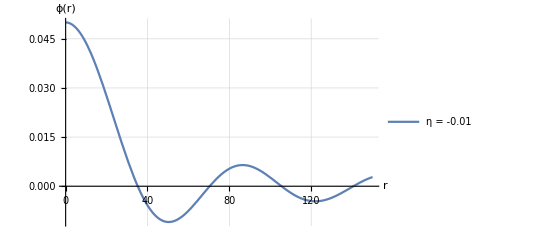

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,150},
Background->White,PlotLegends->Placed[{"η = -0.01"(*, "η = 0.01","η = 0.1"*), "η = -0.05","η = -0.09"(*, "η = -0.01","η = -0.1"*), "η = -0.2","η = -0.05",,"η = -0.05"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
L1=1; η=-0.05;ϕ0=0.5;(* 1.566147319255175890 "1.565204085944661880" *)
k=1/16/ π;mS=1;rMin=0.001; w="1.002057692316372000"(*1.005635727502066000*); rMax=1000; α=1;
s2=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

#### asintótico

```mathematica
0.5*Sqrt[0.09]
```

0.15

```mathematica
L1=1; η=-1;ϕ0=0.15;(* 1.566147319255175890 "1.565204085944661880" *)
k=1/16/ π;mS=1;rMin=0.1; w=1.004787095525063000(*1.005635727502066000*); rMax=100000; α=1;
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[{{0.1, 100000.}}, <>]}}

```mathematica
L1=1; η=-0.09;ϕ0=0.5;(* 1.566147319255175890 "1.565204085944661880" *)
k=1/16/ π;mS=1;rMin=0.1; w=1.004787095525063000(*1.005635727502066000*); rMax=100000; α=1;
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[{{0.1, 100000.}}, <>]}}

```mathematica
func[r_]:=(2 c1 Cos[r Sqrt[Abs[1-w^2]]-1.5])/r
```

```mathematica
Evaluate[φ[50]/.s1]
```

{-0.108671}

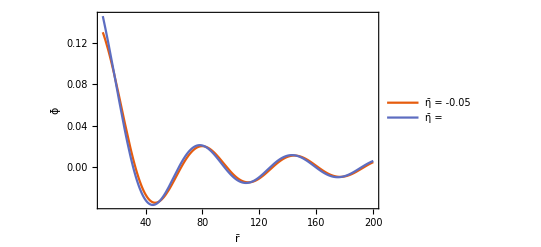

```mathematica
Plot[{Evaluate[φ[r]/.s1],func[r]/.c1->2.8*Sqrt[0.09]},{r,10,200},
Background->White,PlotLegends->Placed[{ "η̄ = -0.05","η̄ = "},{0.75,0.65}],
PlotRange->Full,
GridLines->None,FrameLabel->{"r̄","ϕ̄"},BaseStyle->14,PlotTheme->{"Scientific","Detailed"},PlotStyle->{Automatic,Automatic,{Black,Dashed}}]
```

```mathematica
func2[r_]:=2 c1 Cos[r Sqrt[Abs[1-w^2]]-1.5]
```

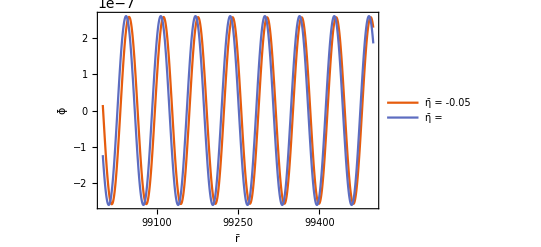

```mathematica
Plot[{Evaluate[φ[r]/.s1],func2[r]/.c1->1.3*10^-7},{r,99000,99500},
Background->White,PlotLegends->Placed[{ "η̄ = -0.05","η̄ = "},{0.75,0.65}],
PlotRange->Full,
GridLines->None,FrameLabel->{"r̄","ϕ̄"},BaseStyle->14,PlotTheme->{"Scientific","Detailed"},PlotStyle->{Automatic,Automatic,{Black,Dashed}}]
```

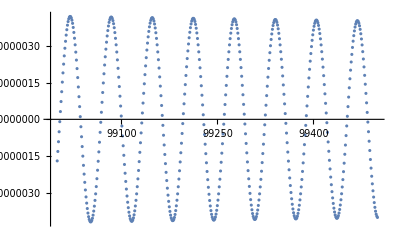

datosXX_Asin_1_p2.dat

```mathematica
datos={};
Do[
AppendTo[datos,{r,Last@Evaluate[φ[r]/.s1]}],{r,99000,99500,1}]
ListPlot[datos,PlotRange->All]
Export["datosXX_Asin_1_p2.dat",datos]
```

```mathematica
LightOrange
```

RGBColor[1, 0.9, 0.8]

### Solitones

#### Shooting

```mathematica
{-1,1.5, 0.568778026578377680,15,0.01,2},{-1,0.75,"0.744851633056108100",15,0.01,2},
```

```mathematica
{1.,0.8,0.993223876953125,20.061000000000053,0.001,3.},{1.,0.6,0.9995159912109375,20.061000000000043,0.001,3.},
```

```mathematica
Amp={ 0.76, 0.74, 0.72, 0.7, 0.68, 0.66, 0.64, 0.62};
Dat={};
η=1;
mS=1;
```

```mathematica
rMin=10^-3;
rMax=15;
UP=0.9995159912109375;(**)
LOW=0.994796905517578;
```

```mathematica
For[i=1,i<Length[Amp]+1,i++,
ϕ0=Amp[[i]]; 
ϕFlat=0;
rStart=rMin;(*rMin;*)
Clear[newStart];

(* start interval for search of omega, fixed by hand *)
omUP=UP;
omLOW=LOW;

While[ϕFlat==0,

If[newStart==1, 
newStart=0,
ϕFlat=1 ];

For[rTest =rStart+0.03(*rStart*), rTest <rMax+0.03,rTest+=0.1,
(*Print[rTest];*)
If[newStart==1,Break[]]; (* reiniciando rStart con el nuevo valor donde explotó *)

(*Print["rTest= ", rTest];*)
stop=0;

While[stop==0,

Which[ MemoryInUse[] > 5*10^19, (* Controlando la memoria *)
Speak["Mem Oree Full Lee Occupied"];
Print["Memory Full! \n"];ϕFlat=1;Break[],
SetPrecision[(omUP-omLOW)/2,prec]<10^-prec, (* Fijando la maxima precision *)
Speak["Maximum Precision Reached"];
Print["Max.Precision Reched! \n"];ϕFlat=1;Abort[]
           ];

w=(omLOW+omUP)/2;

(*Print[w];*)

s=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rTest+1},Method->{"EquationSimplification"->"Residual"}];

stop=1;

Do[
Which[Evaluate[φ[rp]/.s][[1]]>2ϕ0||Evaluate[φ[rp]/.s][[1]]>Evaluate[φ[rp-0.01]/.s][[1]],
stop=0;
Print["Pos"];
omLOW=w;
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[] (* Sale del ciclo Do *),
Evaluate[φ[rp]/.s][[1]]<-2ϕ0||Evaluate[φ[rp]/.s][[1]]<0,
stop=0;
Print["Neg"];
omUP=w;
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[](* Sale del ciclo Do *)
](* End Which*),{rp,rMin+0.03,rTest}
](* End Do *)
](* End While *)
 ](* End For that change the rTest value *)
];(* End While ϕFlat==0 *)
Print["Encontrado"];
Print[w];
AppendTo[Dat,{η,ϕ0,w,rTest,rMin,2}];
](* End For that choose the ϕ0 value *);
```

SetPrecision::precbd: Requested precision prec is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of SetPrecision::precbd will be suppressed during this calculation.

$Aborted

```mathematica
w
```

0.997156

```mathematica
N@Dat
```

{{1.,0.78,0.994797,20.061,0.001,2.}}

```mathematica
datNViable={};
```

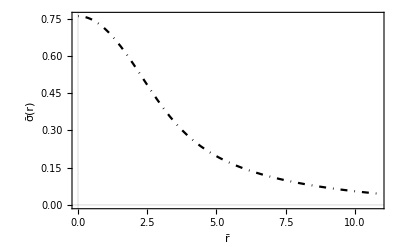

```mathematica
Plot[{Evaluate[φ[x]/.s]},{x,rMin,rTest},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]
```

```mathematica
w=0.7822449547376848
```

0.782245

```mathematica
{1.,2.86,0.770125,15,0.001,3}
```

```mathematica
{{1.,0.78,0.994796905517578,20.061000000000053,0.001,2.}, {1.,0.76,0.9971564483642578,20.061000000000053,0.001,2.}, {1.,0.74,0.997864483642578,30.061000000000053,0.001,2.},{1.,0.7,0.99964483642578,100,0.001,2.}}
```

```mathematica
L1=1; η=1.0;ϕ0=0.65; mS=1;rMin=0.001; w=0.9999999999; rMax=300; α=1;(* .26,1.012476348812271000 *)
s=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

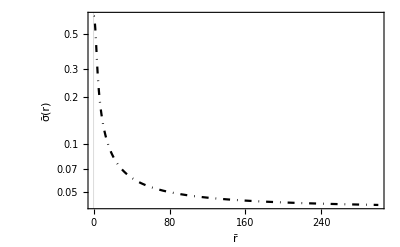

```mathematica
LogPlot[{Evaluate[φ[x]/.s]},{x,rMin,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black}]
```

```mathematica
{-1.,3.3,0.42257696476282125,15.060999999999996,30.,0.001,2.}
```

```mathematica
{-1,3.4,.41793856334,20,0.01,2}
```

```mathematica
L1=1; η=-1;ϕ0=3.4; mS=1;rMin=0.001; w=.41793856334; rMax=13; α=1;(* .26,1.012476348812271000 *)
s=NDSolve[{SeidelEqsList[[1]],ini[[2]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

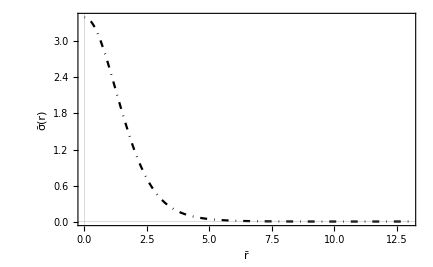

```mathematica
Plot[{Evaluate[φ[x]/.s]},{x,rMin,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black}]
```

#### Test

```mathematica
datViableN[[36]]
```

{-1.,0.42,0.934121,20.061,0.001,2.}

```mathematica
(*η, σ0, w, rMax, rMin, solucion*)
datViableN={(*{-1,200,.1012759251998,30,0.01,2},*){-1,3.4,.41793856334,20,0.01,2},{-1.,3.3,0.42257696476282125,15.060999999999996,30.,0.001,2.},{-1.,3.2,0.42741868345609285,14.060999999999996,0.001,2.},{-1.,3.1,0.4324795011056545,14.060999999999996,0.001,2.},{-1.,3.,0.4377771197616428,14.060999999999996,0.001,2.},{-1.,2.8,0.44916370674928163,14.060999999999996,0.001,2.},{-1.,2.6,0.4617670716752323,14.060999999999996,0.001,2.},{-1.,2.4,0.47582866010220326,14.060999999999996,0.001,2.},{-1.,2.3,0.4835012036913516,16.060999999999996,0.001,2.},{-1.,2.2,0.4916637282838694,16.060999999999996,0.001,2.},{-1.,2.1,0.5003725343240428,16.060999999999993,0.001,2.},{-1.,2.,0.5096931835894678,16.060999999999996,0.001,2.},{-1.,1.9,0.5197030004926888,15.060999999999996,0.001,2.},{-1.,1.8,0.5304939359182985,15.060999999999996,0.001,2.},{-1.,1.7,0.5421761948466499,15.060999999999996,0.001,2.},{-1.,1.6,0.5548830819525595,15.060999999999993,0.001,2.},{-1,1.5, 0.568778026578377680,15,0.01,2},{-1.,1.4,0.5840631169311036,15.060999999999996,0.001,2.},{-1.,1.3,0.6009934845506101,15.060999999999996,0.001,2.},{-1.,1.2,0.619894290301,15.06099999999999,0.001,2.},{-1.,1.1,0.6411891648478545,15.060999999999993,0.001,2.},{-1.,1.,0.6654413468170933,15.060999999999993,0.001,2.},{-1.,0.9,0.693418571871145,15.060999999999996,0.001,2.},{-1.,0.8,0.7261983250296968,15.060999999999996,0.001,2.},{-1,0.75,"0.744851633056108100",15,0.01,2},{-1.,0.74,0.7487935716572761,13.060999999999993,0.001,2.},{-1.,0.73,0.7528113814447068,13.060999999999993,0.001,2.},{-1.,0.72,0.7569073493158587,13.060999999999993,0.001,2.},{-1.,0.71,0.7610840312149496,13.060999999999993,0.001,2.},{-1.,0.7,0.7653439830861977,13.060999999999996,0.001,2.},{-1.,0.69,0.769690164443961,13.060999999999996,0.001,2.},{-1.,0.68,0.774125400279217,13.060999999999996,0.001,2.},{-1.,0.67,0.7786527846297033,13.060999999999993,0.001,2.},{-1.,0.66,0.7832754115331583,13.060999999999996,0.001,2.},{-1.,0.65,0.7879966440740788,13.060999999999996,0.001,2.},{-1.,0.64,0.7928201143837219,13.060999999999996,0.001,2.},{-1.,0.63,0.7977491855465857,13.060999999999996,0.001,2.},{-1.,0.62,0.8027878932640666,13.060999999999996,0.001,2.},{-1.,0.61,0.807940407760942,13.060999999999993,0.001,2.},{-1.,0.5959478335634352,0.8153806268563724,20,0.001,2},{-1.,0.58,0.824121853877925,15.060999999999996,0.001,2.},{-1.,0.56,0.8355594207274031,15.060999999999996,0.001,2.},{-1.,0.54,0.8475642898925049,15.060999999999996,0.001,2.},{-1.,0.52,0.8601807891916667,15.060999999999996,0.001,2.},{-1.,0.5051081756979723,0.87,20.750000000000444,0.01,2},{-1.,0.49,0.8803566619724883,20.061000000000053,0.001,2.},{-1.,0.48,0.887440805415177,20.061000000000014,0.001,2.},{-1.,0.46,0.9021844880215562,20.061000000000014,0.001,2.},{-1.,0.44,0.9177340182101899,20.061000000000014,0.001,2.},{-1.,0.42,0.9341209267802149,20.061000000000014,0.001,2.},{-1.,0.4,0.9513371701748521,20.061000000000014,0.001,2.},{-1,0.385,0.964900484864190000,20,0.001,2},{-1.,0.38,0.96925773469264,20.06100000000003,0.001,2.},{-1.,0.37,0.978358703464759,20.061000000000053,0.001,2.},{-1.,0.36,0.9873308491984716,20.061000000000043,0.001,2.},{-1,0.35,0.995939259294331000,20,0.01,2}, {-1,0.3415,0.999999999878928000,200,0.01,2}};
```

```mathematica
(*{-1.,0.47,0.894714727586198,20.06100000000003,0.001,2.},*)(*{-1.,0.45,0.9098561066616876,20.061000000000014,0.001,2.},*)
(*{-1.,0.43,0.9258216957640117,20.06100000000003,0.001,2.},*)(*{-1.,0.41,0.9426288603779158,20.061000000000014,0.001,2.},*)(*,{-1.,0.75,0.7448516414638193,13.060999999999996,0.001,2.}*)
```

```mathematica
datViableP={{1.,2.86,0.770125,15,0.001,3},{1.,2.84,0.7716365872185278,11.060999999999979,0.001,3},{1.,2.82,0.7730806347642878,11.060999999999996,0.001,3},{1.,2.8,0.7745851308119633,11.06099999999999,0.001,3},{1.,2.78,0.7761135077492844,15.060999999999996,0.001,3},{1.,2.75,0.7783938415288926,15.060999999999993,0.001,3},{1.,2.72,0.7806964843749999,15.060999999999996,0.001,3},{1.,2.7,0.7822449547376848,25.06100000000003,0.001,3},{1.,2.65,0.7861634957974358,20.06100000000003,0.001,3},{1.,2.6,0.7901528317678485,20.06100000000003,0.001,3},{1.,2.55,0.7942159830927848,20.061000000000014,0.001,3},{1.,2.5,0.7983558304429055,20.061000000000014,0.001,3},{1.,2.45,0.8025751978497895,20.061000000000014,0.001,3},{1.,2.4,0.8068768902870114,20.06100000000003,1.,0.001,3},{1.,2.35,0.8112637252807617,20.061000000000057,0.001,3},{1.,2.3,0.815738507270813,20.06100000000003,0.001,3},{1.,2.25,0.8203041187143326,20.06100000000003,0.001,3},{1.,2.2,0.8249636300778389,20.061000000000014,0.001,3},{1.,2.15,0.8297198441228915,20.061000000000014,0.001,3},{1.,2.1,0.8345757556261,20.06100000000003,0.001,3},{1.,2.,0.8445988314188136,20.061000000000057,0.001,3},{1.,1.9,0.8550566563002961,20.061000000000014,0.001,3.},{1.,1.8,0.8659721308804422,20.06100000000003,0.001,3.},{1,1.7641566171439984,0.87,28.170000000001604,0.001,3},{1.,1.7,0.8773653287038905,20.061000000000043,0.001,3.},{1.,1.6,0.889251053382468,20.061000000000014,0.001,3.},{1.,1.5,0.9016344451904297,20.061000000000014,0.001,3},{1.,1.4,0.9145037841796875,20.061000000000043,0.001,3},{1.,1.3,0.9278173828125001,20.061000000000053,0.001,3},{1.,1.2,0.9414862060546874,20.061000000000014,0.001,3},{1.,1.1,0.9553353917598724,20.061000000000043,0.001,3.},{1.,1.,0.9690234375,20.06100000000003,0.001,3},{1.,0.9,0.9818496704101562,20.06100000000003,0.001,3.},{1.,0.8,0.993223876953125,20.061000000000053,0.001,3.},(*{1.,0.7,0.9980639648437499,20.061000000000053,0.001,3.},*){1.,0.78,0.994796905517578,20.061000000000053,0.001,2.}, {1.,0.76,0.9971564483642578,20.061000000000053,0.001,2.}, {1.,0.74,0.997864483642578,30.061000000000053,0.001,2.},{1.,0.7,0.99964483642578,100,0.001,2.},{1,0.6825, 0.999990234375000000,200,0.001,3},(*{1,0.682,0.99999999999,200,0.001,3},*){1.,0.6,0.9995159912109375,20.061000000000043,0.001,3.}};
```

```mathematica
dat3={};
dat2={};
Do[AppendTo[dat3,{datViableP[[i,3]],datViableP[[i,2]]}];
AppendTo[dat2,datViableP[[i,2]]],{i,1,Length[datViableP]}]
```

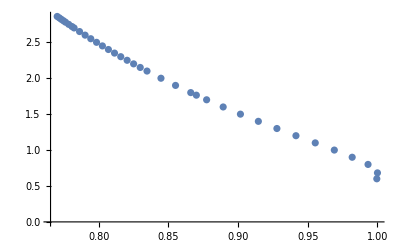

```mathematica
ListPlot[{dat3},Joined->False,PlotRange->All]
```

```mathematica
dat3
```

```mathematica
Export["XX_P_solR.dat",dat3]
```

XX_P_solR.dat

```mathematica
ClearAll[rMin]
```

```mathematica
2.86,0.770125,
```

```mathematica
L1=1; η=1.0;ϕ0=3.0; mS=1;rMin=0.001; w=0.700125; rMax=60; α=1;(* .26,1.012476348812271000 *)
s3=NDSolve[{SeidelEqsList[[1]],ini[[1]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

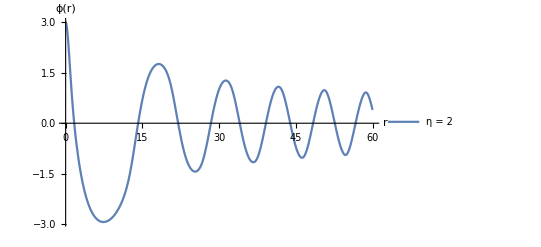

```mathematica
Plot[{Evaluate[φ[r]/.s3]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 2","η = 1","η = 0"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->None]
```

```mathematica
L1=1; η=1.0;ϕ0=2.7; mS=1;rMin=0.001; w=0.7822449547376848; rMax=30; α=1;(* .26,1.012476348812271000 *)
s3=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

```mathematica
L1=1; η=1.0;ϕ0=0.682; mS=1;rMin=0.001; w=0.99999999999; rMax=100; α=1;(* .26,1.012476348812271000 *)
s3=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}]
```

{{φ→InterpolatingFunction[…]}}

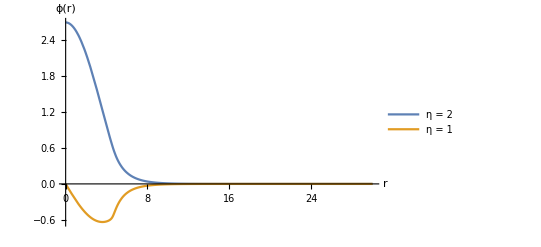

```mathematica
Plot[{Evaluate[φ[r]/.s3],Evaluate[φ'[r]/.s3]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 2","η = 1","η = 0"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->None]
```

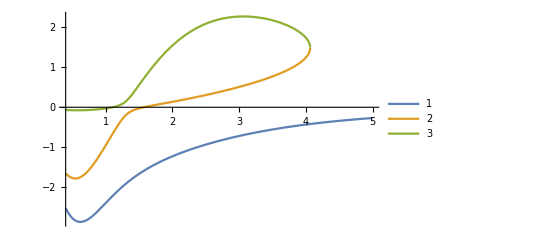

```mathematica
Plot[{Evaluate[φ'[r]]/.s,Evaluate[-(22 r w^2 φ[r]+√(r^2 (9+412 w^4 φ[r]^2+r^2 (4 w^2-32 w^6 φ[r]^2))))/(18+8 r^2 w^2)]/.s,Evaluate[(-22 r w^2 φ[r]+√(r^2 (9+412 w^4 φ[r]^2+r^2 (4 w^2-32 w^6 φ[r]^2))))/(18+8 r^2 w^2)]/.s},{r,0.4,5},PlotLegends->Automatic]
```

```mathematica
ClearAll[w]
```

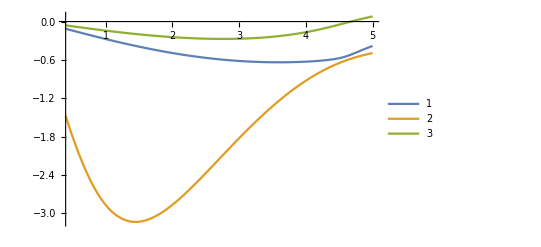

```mathematica
Plot[{Evaluate[φ'[r]]/.s3,Evaluate[-(22 r w^2 φ[r]+√(r^2 (9+412 w^4 φ[r]^2+r^2 (4 w^2-32 w^6 φ[r]^2))))/(18+8 r^2 w^2)]/.s3,Evaluate[(-22 r w^2 φ[r]+√(r^2 (9+412 w^4 φ[r]^2+r^2 (4 w^2-32 w^6 φ[r]^2))))/(18+8 r^2 w^2)]/.s3},{r,0.4,5},PlotLegends->Automatic]
```

```mathematica
L1=1; η=1.0;ϕ0=2.7; mS=1;rMin=0.001; w=0.7822449890159435; rMax=20; α=1;(* .26,1.012476348812271000 *)
s2=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}]
```

{{φ→InterpolatingFunction[…]}}

```mathematica
L1=1; η=1.0;ϕ0=3.0; mS=1;rMin=0.001; w=0.9879822449890159435; rMax=800; α=1;(* .26,1.012476348812271000 *)
s1=NDSolve[{SeidelEqsList[[1]],ini[[2]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}]
```

{{φ→InterpolatingFunction[…]}}

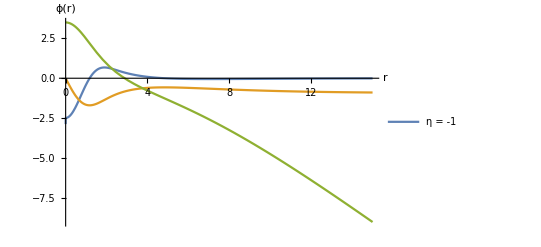

```mathematica
Plot[{Evaluate[φ''[r]/.s3],Evaluate[φ'[r]/.s3],Evaluate[φ[r]/.s3]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -1"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->None]
```

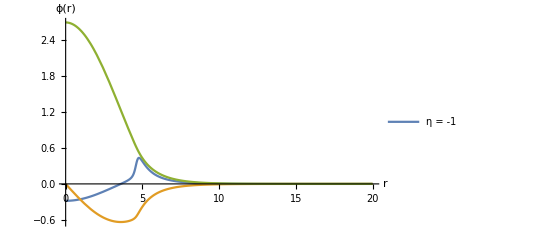

```mathematica
Plot[{Evaluate[φ''[r]/.s2],Evaluate[φ'[r]/.s2],Evaluate[φ[r]/.s2]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -1"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->None]
```

```mathematica
Table[
AA=minϕ0critBHplus[[i]];
L1=1;
η=AA[[1]];(* cambiar*)
ϕ0=AA[[2]]; 
α=1;
k=1/16/ π;mS=1;rMin=10^-3; rMax=25;
w=0.996540169109419000;

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{Evaluate[φ[rMax]/.s]},
PlotRange->All,AxesOrigin->{0,0},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic],{i,1,Length[minϕ0critBHplus]}]
```

```mathematica
{1.,0.9,0.9818496704101562,20.06100000000003,0.001,3.}
```

```mathematica
{-1.,0.9,0.693418571871145,15.060999999999996,0.001,2.},
```

```mathematica
L1=1; η=1.0;ϕ0=0.9; mS=1;rMin=0.001; w=0.9818496704101562; rMax=20; α=1;(* .26,1.012476348812271000 *)
s1=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];

L1=1; η=-1.0;ϕ0=0.9; mS=1;rMin=0.001; w=0.693418571871145; rMax=15; α=1;(* .26,1.012476348812271000 *)
s2=NDSolve[{SeidelEqsList[[1]],ini[[2]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];
```

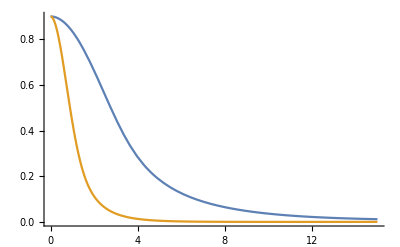

```mathematica
Plot[{Evaluate[φ[r]]/.s1, Evaluate[φ[r]]/.s2},{r,rMin,15},PlotRange->All]
```

```mathematica
datN={};
datP={};
Do[
AppendTo[datN,{r,(Evaluate[φ[r]]/.s2)[[1]] }];
AppendTo[datP,{r,(Evaluate[φ[r]]/.s1)[[1]] }],
{r,rMin,15,0.01}
]
```

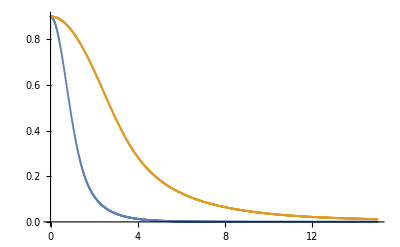

```mathematica
ListPlot[{datN,datP},PlotRange->All]
```

```mathematica
Export["XX_P_ProfBH.dat",datP]
Export["XX_N_ProfBH.dat",datN]
```

XX_P_ProfBH.dat

XX_N_ProfBH.dat

#### asintotico2

```mathematica
L1=1; η=1;ϕ0=2.7;
k=1/16/ π;mS=1;rMin=0.001; w=0.7822449890159435; rMax=30; α=1;(* .26,1.012476348812271000 *)
sB=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}]
```

{{φ→InterpolatingFunction[…]}}

```mathematica
Plot[{Evaluate[φ[r]/.sB](*,-Evaluate[φ'[r]/.sB]/(1-r Sqrt[1-w^2])*)},{r,rMin,rMax},
Background->White(*,PlotLegends->Placed[{"η = -1"},{0.85,0.65}],*),
PlotRange->Full,
GridLines->None, AxesOrigin->{0,0},BaseStyle->14,PlotTheme->{"Scientific"},FrameLabel->{"r̄","ϕ̄"}]
```

```mathematica
FindRoot[Evaluate[φ[r]/.sB]==-Evaluate[φ'[r]/.sB]/(1-r Sqrt[1-w^2]),{r,rMin,1.5}]
```

{r→1.3671}

```mathematica
c1=Abs[Evaluate[φ[r]/.sB]]r Exp[r Sqrt[1-w^2]]/.{r->1.3670984155361023}
```

{7.83022}

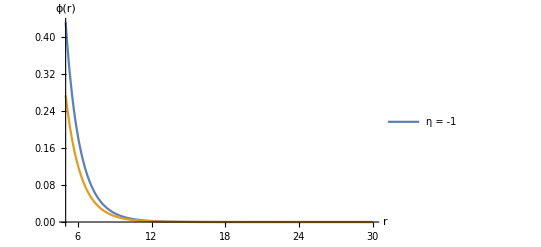

```mathematica
fun[r_]:=Exp[-r Sqrt[1-w^2]]/r c1/.c1-> 30.83
Plot[{Evaluate[φ[r]/.sB], fun[r]},{r,rMin+5,rMax},
Background->White,PlotLegends->Placed[{"η = -1"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"}]
```

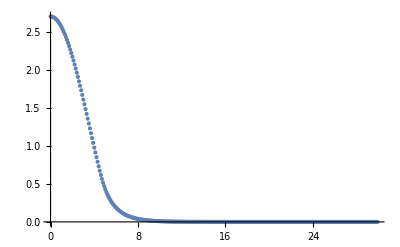

datosXX_Asin_2.dat

```mathematica
datos={};
Do[
AppendTo[datos,{r,Last@Evaluate[φ[r]/.sB]}],{r,rMin,rMax,0.1}]
ListPlot[datos,PlotRange->All]
Export["datosXX_Asin_2.dat",datos]
```